```mathematica
n=100
m=100
Sentro[na_]:=Log[n!*m^(n-na)/((n-na)!*na!)]
Sentrosterl[na_]:=n*Log[n]-n+(n-na)*Log[m]-na*Log[na]+na-(n-na)*Log[n-na]+(n-na)
Sentro[0]//N
```

100

100

460.517

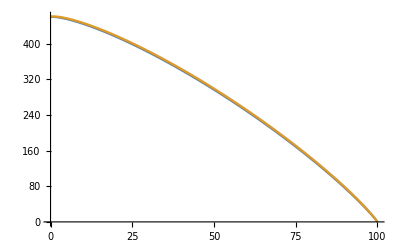

```mathematica
Energie[na_,gamma_]:=-na-gamma*na^2/n
Plot[{Sentro[na], Sentrosterl[na]},{na,0,100}]
```

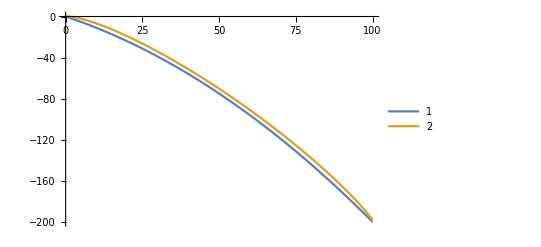

```mathematica
Plot[{Energie[na,1],0.43*Sentro[na]-0.43*Sentro[0]},{na,0,100}, PlotLegends->Automatic]
```

```mathematica
eneder[na_]:=D[Energie[na,1],na]
entroder[na_]:=D[0.43*Sentro[na]-0.43*Sentro[0],na]
```

```mathematica
eneder[x]
```

-1-x/50

```mathematica
entroder[x]/.x->50
```

-1.98022

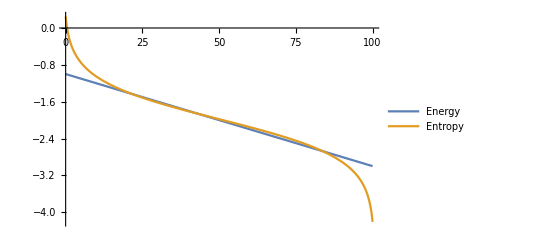

```mathematica
Plot[{eneder[x]/.x->na,entroder[x]/.x->na},{na,0,100}, PlotLegends->{"Energy","Entropy"}, PlotRange->Automatic]
```

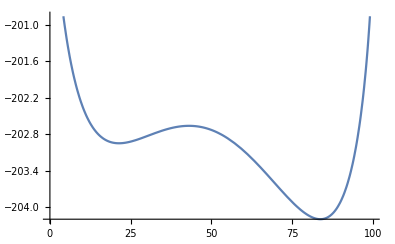

```mathematica
Freeenergie[na_,temper_,gamma_]:=Energie[na,gamma]-temper*Sentro[na]
Plot[{Freeenergie[na,0.43,1]},{na,0,100}, PlotRange->Automatic]
```

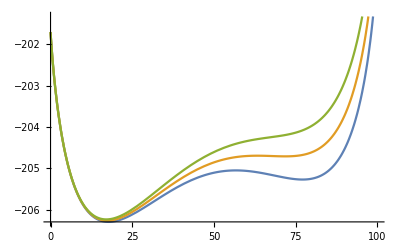

```mathematica
Plot[{Freeenergie[na,0.438,1],Freeenergie[na,0.438,0.99],Freeenergie[na,0.438,0.98]},{na,0,100}]
```